```mathematica
f[x_,s_]:=x UnitStep[s-x]+s(1-x)/(1-s)UnitStep[x-s]
```

```mathematica
a[n_,s_]=2Integrate[f[x,s]Sin[π n x],{x,0,1}]
```

1/(n^2 π^2 (-1+s))2 (-s UnitStep[1-s] (-n π (-1+s) Cos[n π s]-Sin[n π]+Sin[n π s]+(n π+n π (-1+s) Cos[n π s]-Sin[n π s]) UnitStep[-s])+(-1+s) (-n π s Cos[n π s]+Sin[n π s]+(-n π Cos[n π]+n π s Cos[n π s]+Sin[n π]-Sin[n π s]) UnitStep[-1+s]) UnitStep[s])

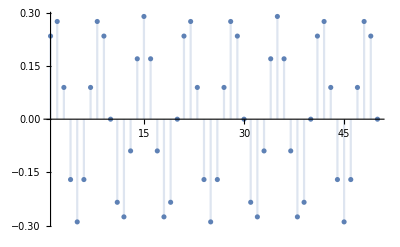

```mathematica
DiscretePlot[n^2%6/.s->0.3,{n,50},PlotRange->All]
```

```mathematica
Quit[]
```

```mathematica
vw[s_,t_,tone_]:=Table[Sum[1/(n^2 π^2 (-1+s))2 (-s UnitStep[1-s] (-n π (-1+s) Cos[n π s]-Sin[n π]+Sin[n π s]+(n π+n π (-1+s) Cos[n π s]-Sin[n π s]) UnitStep[-s])+(-1+s) (-n π s Cos[n π s]+Sin[n π s]+(-n π Cos[n π]+n π s Cos[n π s]+Sin[n π]-Sin[n π s]) UnitStep[-1+s]) UnitStep[s])Cos[2π 440.n 2^(tone/12)τ],{n,1,100}],{τ,0,t,1./48000}]
```

```mathematica
Table[NSum[τ,{n,1,10}],{τ,0,1,0.01}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.}

```mathematica
Monitor[vw[0.25,1.,0.];,τ]
```

```mathematica
Monitor[vw[0.5,1.,0.];,τ]
```

```mathematica
%30[[163]]
```

-0.264147

```mathematica
Sound[SampledSoundList[%14,48000]]
```

-Graphics-

```mathematica
%14[[1]]
```

$Aborted